## Генератор Геффа

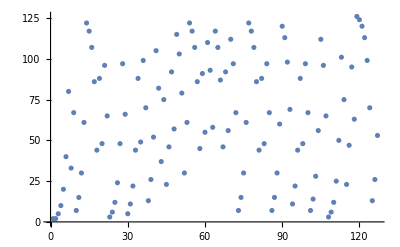
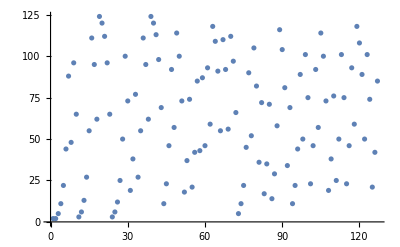
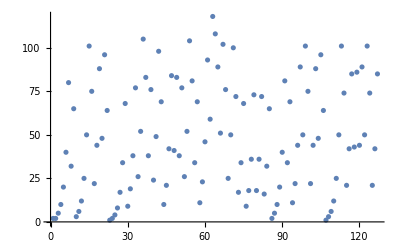
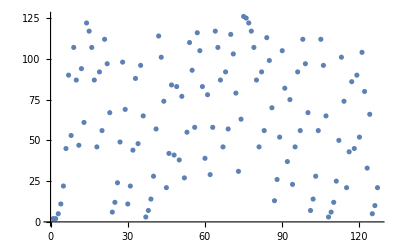
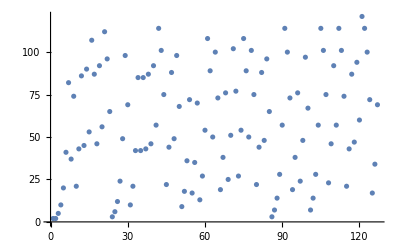
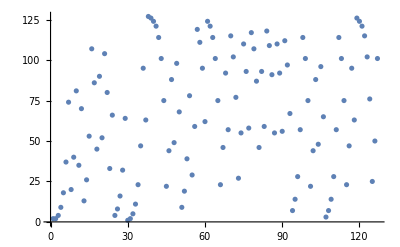
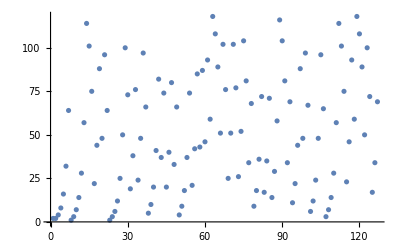
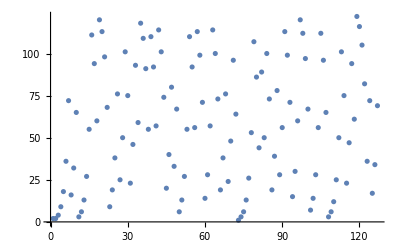
{{-Graphics-,c3=45},{-Graphics-,c3=49},{-Graphics-,c3=53},{-Graphics-,c3=57},{-Graphics-,c3=61},{-Graphics-,c3=65},{-Graphics-,c3=69},{-Graphics-,c3=73},{-Graphics-,c3=77},{-Graphics-,c3=81},{-Graphics-,c3=85},{-Graphics-,c3=89},{-Graphics-,c3=93},{-Graphics-,c3=97},{-Graphics-,c3=101},{-Graphics-,c3=105},{-Graphics-,c3=109},{-Graphics-,c3=113},{-Graphics-,c3=117},{-Graphics-,c3=121},{-Graphics-,c3=125}}

```mathematica
nMax=1024;
x1=11;
x2=52;
x3=34;
c1=37;
c2=101;
p=7;

BaseForm[c1,2];
BaseForm[c2,2];
modulo=2^p;(* модуль *)
lfsrStep[x_,c_,m_]:=Mod[
BitOr[BitShiftLeft[x,1],Mod[DigitCount[BitAnd[x,c],2,1],2]],
m];(*шаг вычислений*)
X1*X2+X2*X3+X3
geffStep[x1_,x2_,x3_]:=BitXor[BitAnd[x1,x2],BitAnd[x2,x3],x3];
geff[x1_,x2_,x3_,c1_,c2_,c3_,m_]:=RecurrenceTable[{X[n+1]==geffStep[X1[n],X2[n],X3[n]],X[1]==geffStep[x1,x2,x3],X1[n+1]==lfsrStep[X1[n],c1,m],X1[1]==x1,X2[n+1]==lfsrStep[X2[n],c2,m],X2[1]==x2,X3[n+1]==lfsrStep[X3[n],c3,m],X3[1]==x3},X,{n,1,modulo-1},DependentVariables->{X,X1,X2,X3}];

Table[{ListPlot[geff[x1,x2,x3,c1,c2,c,modulo]],"c3="~~ToString[c]},{c,45,128,4}]
```

```mathematica
Table[
ArrayPlot[
Partition[
PolynomialMod[geff[x1,x2,x3,c1,c2,i,modulo],2],
7,1]],
{i,modulo-1}
]
```

{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}